```mathematica
Clear[orbit];Clear[eqns];Clear[soln];
(*fudge an orbit*)


tend = 12;
eartht=12; (*this was tend*)
translength = 0.06;
solart = eartht/12;
t0=0.34eartht; 
t1=t0 + translength eartht;
t2= 0.4 eartht; (*time when white line starts to plot*)
t3= t2+3solart; (*time when the last part of the while line disappears*)
t4 = t0 + 4solart;
t5=  t4+ translength eartht;
tellipse1 = 1.12;
tellipse2 = 3.18;
tellipse3 = 1.12 + 2*4;
tellipse4 = 3.18+ 2*4;

psptimedilation = 1.14559 (*The orbit is just an ellipse, not based on gravity or mass of sun, so I can fix its rate around the ellipse to make the animation loop*)

{x0,y0}={-1,1};{v0x,v0y}={0.3,0.3};
eqns={x[0]==x0,y[0]==y0,x'[0]==v0x,y'[0]==v0y,x''[t]==-x[t]/(x[t]^2+y[t]^2)^1.5,y''[t]==-y[t]/(x[t]^2+y[t]^2)^1.5};
soln=Map[Head,{x[t],y[t]}/. First[NDSolve[eqns,{x[t],y[t]},{t,0,tend*psptimedilation}]]];

earth={-Cos[2 Pi #/eartht],Sin[2 Pi #/eartht]}&;
solar={-Cos[2 Pi #/solart],Sin[2 Pi #/solart]}&;
psp[t_]:={soln[[1]][t*psptimedilation],soln[[2]][t *psptimedilation]};
bg=RGBColor[0.,0.05,0.1];
smoothstep[t_,t0_,t1_]:=With[{tt=(t-t0)/(t1-t0)},If[tt<0,0,If[tt>1,1,6 tt^5-15 tt^4+10 tt^3]]];
smoothstepI[t_,t0_,t1_]:=If[(t-t0) (t0-t1)>0,0,If[(t-t1) (-t0+t1)>0,1/2 (2 (t-t1)+t1-t0),-(((t-t0)^4 (2 t^2+t0^2+2 t (t0-3 t1)-4 t0 t1+5 t1^2))/(2 (t0-t1)^5))]];

nstars=30;
stars= RandomReal[{-3,3},{nstars,2}];
starsizes=RandomReal[{0,1},nstars];

rspiralcar[t_, theta_, a_] := FromPolarCoordinates[a*theta + 2 Pi t];


transform[T_]:=RotationTransform[2 Pi (smoothstepI[T/solart,t0,t1]-smoothstepI[T/solart,t4,t5]),{0,0}].
ScalingTransform[(1+0.2 (smoothstep[T/solart,t0,t1]-smoothstep[T/solart,t4,t5])) {1,1}];
daylight[p_,r_,col_]:={Lighter@col,Disk[p,r],Darker@col,EdgeForm[],GeometricTransformation[Disk[p,r,{0,Pi}],RotationTransform[{{0,1},Normalize[p]},p]]};
pspscale = 0.05;pol = Polygon[{{-1 pspscale,0},{-1.5pspscale,-1pspscale},{1.5pspscale,-1pspscale},{1pspscale,0}, {1pspscale,2pspscale},{-1pspscale,2pspscale}}];pspobj[pspp_,col_]:=GeometricTransformation[pol,TranslationTransform[pspp].RotationTransform[{{0,1},Normalize[pspp]}]];
frame[T_]:=(Show[Graphics[{},Background->RGBColor[0.,0.05,0.1],PlotRange->1.8],ParametricPlot[transform[T-t][psp[T-t]],{t,0, Min[eartht,Max[0.001,Min[T-t2 ,2 (t3-T)]]]},PlotStyle->White],ParametricPlot[transform[T-t][psp[T-t]],{t,0, Min[eartht,Max[0.001,Min[T-tellipse1 ,2 (tellipse2-T)]]]},PlotStyle->White],ParametricPlot[transform[T-t][psp[T-t]],{t,0, Min[eartht,Max[0.001,Min[T-tellipse3 ,2 (tellipse4-T)]]]},PlotStyle->White],ParametricPlot[transform[T][RotationTransform[-2 Pi T/solart,{0,0}][2*{t Cos[t], t Sin[t]}]], {t,0,Pi},PlotStyle->White],ParametricPlot[transform[T][RotationTransform[-2 Pi T/solart+ Pi,{0,0}][2*{t Cos[t], t Sin[t]}]], {t,0,Pi},PlotStyle->White],Graphics[GeometricTransformation[{White,{Table[{ColorData["StarryNightColors"][starsizes[[i]]],AbsolutePointSize[1+2 starsizes[[i]]],Point[stars[[i]]]},{i,nstars}]},EdgeForm[Directive[AbsoluteThickness[2],bg]],{RGBColor[1,192/255,0],Disk[{0,0},0.13]},{daylight[earth[T],0.06,RGBColor[0.17,0.59,1.]]},{pspobj[psp[T],RGBColor[1.,0.8,0.65]]}},transform[T]]]]);
Manipulate[frame[T],{T,0,tend}]
```

1.14559

```mathematica
anim = Table[frame[T],{T,0,tend,0.1}];
Export["first_draft.gif", anim]
```

first_draft.gif

```mathematica
SystemOpen["first_draft.gif"]
```

```mathematica
SystemOpen["first_draft.gif"]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["first_draft.gif"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["first_draft.gif"]]]
```

General::sysffmpeg: Using a limited version of FFmpeg. Install FFmpeg to get more complete codec support.

first_draft.mp4

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["first_draft.mp4"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["first_draft.gif"]]]
```

```mathematica
timings = {t0,t1,t2,t3,t4,t5, tend}
```

{4.08,4.8,4.8,7.8,8.08,8.8,12}

```mathematica
psp[0]
```

{-1.,1.}

```mathematica
psp[4*1.14559]
```

```mathematica
{-1.0000087294911009,0.9999859372183536}
```

```mathematica
solart = 1
rspiral[theta_, a_] := a*(theta );
T =0.5
ParametricPlot[transform[T][RotationTransform[2 Pi T/solart,{0,0}][10*{t 0.1 Cos[t], t 0.1 Sin[t]}]], {t,0,Pi}];
ParametricPlot[transform[T][RotationTransform[2 Pi T/solart + Pi,{0,0}][10*{t 0.1 Cos[t], t 0.1 Sin[t]}]], {t,0,Pi}];
```

1

0.5

```mathematica
RotationTransform[2 Pi 0.5 /solart,{0,0}]
```

TransformationFunction[(-1. | -1.22465×10^-16 | 0.
1.22465×10^-16 | -1. | 0.
0. | 0. | 1.)]

Polygon[…]

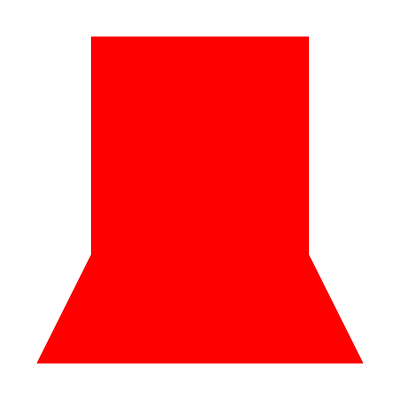

```mathematica
pol = Polygon[{{-1,0},{-1.5,-1},{1.5,-1},{1,0}, {1,2},{-1,2}}]
Graphics[{Red,pol}]
```